```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

## QuantumBasis

```mathematica
QuantumState[{1,2,3,4}]["Basis"]["Association"]
```

<|00→{{1,0},{0,0}},01→{{0,1},{0,0}},10→{{0,0},{1,0}},11→{{0,0},{0,1}}|>

```mathematica
Normal/@QuantumOperator["H"]["InputBasis"]["Association"]
QuantumOperator["H"]["OutputBasis"]["Association"]
```

<|0→{1,0},1→{0,1}|>

<|0→{1,0},1→{0,1}|>

If not specified, we automatically treat everything in the computational basis. Important patterns to remember:

QauntumBasis[{n 1,n 2,...}]

QuantumBasis[n,m]

QuantumBasis[asso]

```mathematica
QuantumBasis[3]["Association"]
```

<|0→{1,0,0},1→{0,1,0},2→{0,0,1}|>

```mathematica
QuantumBasis[2,3]
```

QuantumBasis[…]

```mathematica
QuantumBasis[{3,2,5}]
```

QuantumBasis[…]

```mathematica
QuantumBasis[<|"up"->{1,1},"down"->{1,-ⅈ}|>]["Association"]
```

<|up→{1,1},down→{1,-ⅈ}|>

There are also many named basis types:

```mathematica
QuantumBasis["X"]["Association"]
```

<|ψ_(x_-)→{-1/(√2),1/(√2)},ψ_(x_+)→{1/(√2),1/(√2)}|>

```mathematica
QuantumBasis["Y"]["Association"]
```

<|ψ_(y_-)→{ⅈ/(√2),1/(√2)},ψ_(y_+)→{-ⅈ/(√2),1/(√2)}|>

```mathematica
QuditBasis["X"]["Association"]
```

<|ψ_(x_-)→SparseArray[…],ψ_(x_+)→SparseArray[…]|>

## QuantumState

The most important pattern to remember is QuantumBasis[arg,qb], with qb defining the basis (if not specified, will be treated automatically as a computational basis, given dimensions of arg.

arg: a list of amplitudes, density matrices or named states:

```mathematica
QuantumState[{a,b}]
```

a 0+b 1

```mathematica
QuantumState[{1,ⅈ,3},3]
```

0+ⅈ 1+3 2

Note padding when qb is not specified:

```mathematica
QuantumState[{1,ⅈ,3}]["Amplitudes"]
```

<|00→1,01→ⅈ,10→3,11→0|>

```mathematica
QuantumState[{a,b},"X"]
```

a ψ_(x_-)+b ψ_(x_+)

```mathematica
QuantumState[{a,b}]
```

a 0+b 1

```mathematica
QuantumState[QuantumState[{a,b}],"X"]
```

(-a/(√2)+b/(√2)) ψ_(x_-)+(a/(√2)+b/(√2)) ψ_(x_+)

```mathematica
QuantumState[QuantumState[{a,b}],"X"]==QuantumState[{a,b}]//Simplify
```

{True,True}

```mathematica
QuantumState[{a,b,c,d},{"X","Fourier"}]
```

a ψ_(x_-)F_1+b ψ_(x_-)F_2+c ψ_(x_+)F_1+d ψ_(x_+)F_2

```mathematica
QuantumState[{{a,b},{c,d}},"X"]
```

a ψ_(x_-)ψ_(x_-)+b ψ_(x_-)ψ_(x_+)+c ψ_(x_+)ψ_(x_-)+d ψ_(x_+)ψ_(x_+)

```mathematica
QuditBasis/@Wolfram`QuantumFramework`PackageScope`$QuditBasisNames
```

{QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…],QuditBasis[…]}

```mathematica
QuantumBasis/@Wolfram`QuantumFramework`PackageScope`$QuditBasisNames
```

{QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…]}

```mathematica
QuantumState["RandomMixed"]["BlochSpherePlot"]
```

-Graphics3D-

Named states:

```mathematica
QuantumState["RandomPure",3]
```

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumStateNames
```

{0,Zero,1,One,Plus,Minus,Left,Right,PsiPlus,PsiMinus,PhiPlus,PhiMinus,BasisState,Register,UniformSuperposition,UniformMixture,RandomPure,RandomMixed,GHZ,Bell,W,Werner,Graph,BlochVector}

```mathematica
QuantumState["Bell"]
```

00/(√2)+11/(√2)

```mathematica
QuantumState["GHZ"]
```

000/(√2)+111/(√2)

```mathematica
QuantumState[{"Graph",RandomGraph[{7,10}]}]
```

QuantumState[…]

```mathematica
QuantumCircuitOperator[{"Graph",RandomGraph[{7,10}]}][]
```

QuantumState[…]

```mathematica
QuantumState[{"UniformSuperposition",3}]
```

000/(2 √2)+001/(2 √2)+010/(2 √2)+011/(2 √2)+100/(2 √2)+101/(2 √2)+110/(2 √2)+111/(2 √2)

```mathematica
QuantumState[{"UniformSuperposition",3}]==QuantumOperator["H",{1,2,3}]@QuantumState[{"Register",3}]
```

True

```mathematica
QuantumState[{"Werner",p,2}]["Formula"]
```

1/3 p 0000+1/6 (3-2 p) 0101+1/6 (-3+4 p) 0110+1/6 (-3+4 p) 1001+1/6 (3-2 p) 1010+1/3 p 1111

```mathematica
state=QuantumState[{"Werner",p,2}]
```

1/3 p 0000+1/6 (3-2 p) 0101+1/6 (-3+4 p) 0110+1/6 (-3+4 p) 1001+1/6 (3-2 p) 1010+1/3 p 1111

Some arithmetic with states:

```mathematica
x (a 0+b 1)+y (c 0+d 1)
```

(a x+c y) 0+(b x+d y) 1

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuditBasisNames
Wolfram`QuantumFramework`PackageScope`$QuantumStateNames
Wolfram`QuantumFramework`PackageScope`$QuantumOperatorNames
Wolfram`QuantumFramework`PackageScope`$QuantumChannelNames
Wolfram`QuantumFramework`PackageScope`$QuantumCircuitOperatorNames
Wolfram`QuantumFramework`PackageScope`$QuantumDistances
Wolfram`QuantumFramework`PackageScope`$QuantumEntanglementMonotones
```

{Computational,PauliX,PauliY,PauliZ,X,Y,Z,Bell,Fourier,Identity,Schwinger,Pauli,Dirac,Wigner}

{0,Zero,1,One,Plus,Minus,Left,Right,PsiPlus,PsiMinus,PhiPlus,PhiMinus,BasisState,Register,UniformSuperposition,UniformMixture,RandomPure,RandomMixed,GHZ,Bell,W,Werner,Graph,BlochVector}

{Identity,I,Permutation,Curry,Uncurry,Fourier,InverseFourier,XRotation,YRotation,ZRotation,U,Phase,P,RX,RY,RZ,R,Diagonal,GlobalPhase,PhaseShift,SUM,RootNOT,X,Y,Z,PauliX,PauliY,PauliZ,H,Hadamard,SWAP,RootSWAP,CSWAP,Fredkin,C,Controlled,C0,Controlled0,CX,CY,CZ,CH,CT,CS,CPHASE,CNOT,S,T,V,Toffoli,Deutsch,RandomUnitary,RandomHermitian,Spider,ZSpider,XSpider,Switch,Discard,Multiplexer}

{BitFlip,PhaseFlip,BitPhaseFlip,Depolarizing,AmplitudeDamping,GeneralizedAmplitudeDamping,PhaseDamping}

{Graph,GroverDiffusion,GroverDiffusion0,GroverPhaseDiffusion,GroverPhaseDiffusion0,BooleanOracle,PhaseOracle,BooleanOracleR,Grover,GroverPhase,Grover0,GroverPhase0,Bell,Toffoli,BernsteinVaziraniOracle,BernsteinVazirani,Fourier,InverseFourier,PhaseEstimation,Controlled,Trotterization,Magic}

{Fidelity,RelativeEntropy,Trace,BuresAngle,HilbertSchmidt,Bloch}

{Concurrence,Negativity,LogNegativity,EntanglementEntropy,RenyiEntropy,Realignment}

```mathematica
QuantumOperator[{"U",a,b,c}]
```

Cos[a/2] 00+ⅇ^(ⅈ (b+c)) Cos[a/2] 11-ⅇ^(ⅈ c) 01 Sin[a/2]+ⅇ^(ⅈ b) 10 Sin[a/2]

```mathematica
QuantumOperator[{"U",a,b,c}]["Matrix"]//MatrixForm
```

(Cos[a/2] | -ⅇ^(ⅈ c) Sin[a/2]
ⅇ^(ⅈ b) Sin[a/2] | ⅇ^(ⅈ (b+c)) Cos[a/2])

```mathematica
Normal@SparseArray[{{a,b},{c,d}}]
```

{{a,b},{c,d}}

Basis transformation: a state defined in the computational basis, then transformed into a Pauli-X basis:

```mathematica
state=QuantumState["RandomPure"];
QuantumState[state,"X"]
```

QuantumState[…]

There are a couple of functions one can apply on quantum states:

QuantumPartialTrace
QuantumDistance
QuantumEntangledQ
QuantumEntanglementMonotone

```mathematica
state=QuantumState[{a,b,c,d}]
```

a 00+b 01+c 10+d 11

```mathematica
ρ=QuantumState["RandomMixed"]
```

(1.43535+0. ⅈ) 00-(0.401222+0.922154 ⅈ) 01-(0.401222-0.922154 ⅈ) 10+(1.26738+0. ⅈ) 11

```mathematica
ρ["Operator"]
```

(1.43535+0. ⅈ) 00-(0.401222+0.922154 ⅈ) 01-(0.401222-0.922154 ⅈ) 10+(1.26738+0. ⅈ) 11

```mathematica
QuantumPartialTrace[state,{2}]
```

QuantumState[…]

```mathematica
QuantumPartialTrace[state,{2}]["Operator"]["Formula"]//ComplexExpand//Simplify
```

(a^2+b^2) 00+(a c+b d) 01+a c 10+b d 10+c^2 11+d^2 11

```mathematica
QuantumBasis[{"X","Y"}]
```

QuantumBasis[…]

```mathematica
QuantumPartialTrace[QuantumBasis[{"X","Y"}],{2}]
```

QuantumBasis[…]

For example, Werner states with p>=1/2 are not entangled, while p<1/2 are:

```mathematica
QuantumState[{"Werner",1/2,2}]
```

QuantumState[…]

```mathematica
QuantumEntangledQ@QuantumState[{"Werner",1/2,2}]
```

False

```mathematica
QuantumEntangledQ@QuantumState[{"Werner",1/4,2}]
```

True

```mathematica
QuantumEntangledQ[QuantumState["GHZ"]]
```

True

```mathematica
QuantumEntangledQ[QuantumState["GHZ"],{{1},{2}}]
```

False

The following metrics are supported with the QuantumEntanglementMonotone function: Concurrence (default), EntanglementEntropy, LogNegativity, Negativity, {“RenyiEntropy”, α} and Realignment:

```mathematica
QuantumEntanglementMonotone[QuantumState[{"Werner",1/4,2}]]
```

1/2

```mathematica
QuantumEntanglementMonotone[QuantumState[{"Werner",1/4,2}],"LogNegativity"]
```

Log[3/2]/Log[2]

```mathematica
QuantumEntanglementMonotone[QuantumState[{"Werner",1/2,2}],"LogNegativity"]
```

0

```mathematica
QuantumState[{1,2,3,4},4]["Bipartition"]==QuantumState[{1,2,3,4},4]
```

True

```mathematica
QuantumState[RandomReal[{0,1},12],12]["Bipartition",12]
```

QuantumState[…]

```mathematica
QuantumState["RandomPure"]["PureStateQ"]
```

True

```mathematica
QuantumState["RandomPure"]["MatrixState"]
```

QuantumState[…]

```mathematica
QuantumState["RandomPure"]["MatrixState"]["PureStateQ"]
```

True

```mathematica
QuantumState["RandomMixed"]["PureStateQ"]
```

False

```mathematica
QuantumState[{{a,b},{c,d}}]
```

QuantumState[…]

There are lots of interesting properties one can get from a quantum state, such as StateVector, DensityMatrix, Tensor, Norm, TraceNorm, SchmidtBasis, Conjugate, Transpose (and partial transpose), Purify (and Unpurify), Bend (and Unbend) and Bipartition:

```mathematica
QuantumState["RandomMixed"]["Properties"]
```

{Amplitudes,Association,Basis,Bend,BendDual,Bipartition,BlochCartesianCoordinates,BlochPlot,BlochSphericalCoordinates,Computational,Conjugate,ConjugateTranspose,Decompose,DensityMatrix,Diagram,Dimension,Dimensions,Disentangle,Double,Dual,Eigenstates,Eigenvalues,Eigenvectors,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,Entropy,FinalParameters,Formula,FullInputQudits,FullOutputQudits,FullQudits,HasInputQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputQudits,InputRank,InputSize,InputTensor,Kind,Label,LabelHead,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixRepresentation,MatrixState,Mixed,MixedStateQ,NameDimensions,Names,Norm,NormalElementNames,NormalizedAmplitudes,NormalizedDensityMatrix,NormalizedOperator,NormalizedProjector,NormalizedQ,NormalizedState,NormalizedStateVector,Number,Operator,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,Picture,PrimeBasis,Probabilities,Projector,Projectors,Pure,PureEffects,PureMaps,PureStateQ,PureStates,Purify,Purity,QuditBasis,Qudits,Rank,Reverse,ReverseInput,ReverseOutput,SchmidtBasis,Simplify,Size,SpectralBasis,State,StateMatrix,StateTensor,StateType,StateVector,Tensor,TensorDimensions,TensorRepresentation,TensorReverseInput,TensorReverseOutput,Trace,TraceNorm,Transpose,Type,Unbend,UniformBasis,Unpurify,VectorState,VonNeumannEntropy,Weights}

Some of these properties return a numerical value (such as entropy) and some return a quantum state (such as transpose or bipartition).

Generate a random pure state of 2-qubits:

```mathematica
r=QuantumState[{"RandomPure",2}]
```

QuantumState[…]

Decompose it (iteration of Schmidt decomposition until getting separable terms; i.e. no entanglement):

```mathematica
Map[#["Computational"]["Formula"]&,r["Decompose"],{2}]
```

{{(1.40037+0. ⅈ) 0+(0.933796+0.0566596 ⅈ) 1,(-0.204895-0.463097 ⅈ) 0-(0.528795+0.681128 ⅈ) 1},{(-0.124962+0. ⅈ) 0+(0.186712+0.011329 ⅈ) 1,(0.853005-0.126259 ⅈ) 0-(0.468267-0.192786 ⅈ) 1}}

```mathematica
Map[#["Formula"]&,r["Decompose"],{2}]
```

{{1.20356 u_1,v_1},{0.705064 u_2,v_2}}

```mathematica
Total[QuantumTensorProduct/@r["Decompose"]]==r
```

True

Similar operator, but final terms are still 2-qubit states (but separable):

```mathematica
#["Formula"]&/@r["Disentangle"]
```

{1.20356 u_1 v_1,0.705064 u_2 v_2}

```mathematica
Total[r["Disentangle"]]==r
```

True

```mathematica
r=QuantumState["RandomMixed",{3}]
```

QuantumState[…]

```mathematica
r["Purify"]
```

QuantumState[…]

Partial tracing over ancillary qudit returns the original state:

```mathematica
QuantumPartialTrace[%,{2}]==r
```

True

Permute:

```mathematica
QuantumState[{a1,a2,a3,a4}]
```

a1 00+a2 01+a3 10+a4 11

```mathematica
QuantumState[{a1,a2,a3,a4}]["Permute",Cycles[{{1,2}}]]
```

a1 00+a3 01+a2 10+a4 11

An operation can be defined by states (|a><b| format of QM) or an operator (difference in our framework: input/output qudits):

```mathematica
QuantumState["PhiPlus"]
```

00/(√2)+11/(√2)

```mathematica
QuantumState["PhiPlus"]["Projector"]
```

1/2 0000+1/2 0011+1/2 1100+1/2 1111

```mathematica
QuantumState["PhiPlus"]
```

QuantumState[…]

```mathematica
QuantumState["PhiPlus"]["Projector"]
```

1/2 0000+1/2 0011+1/2 1100+1/2 1111

```mathematica
QuantumOperator[QuantumState["PhiPlus"]["Projector"]]
```

1/2 0000+1/2 0011+1/2 1100+1/2 1111

```mathematica
proj=QuantumState["PhiPlus"]["Projector"]
op=QuantumState["PhiPlus"]["Operator"]
```

QuantumState[…]

QuantumOperator[…]

```mathematica
r=QuantumState[{"RandomPure",2}];
```

```mathematica
proj[r]==QuantumState["PhiPlus"]
```

```mathematica
op[r]==QuantumState["PhiPlus"]
```

Quantum state is a tensor flow with no input and one or more outputs (depending on the number of qudits):

```mathematica
QuantumState["1"]
```

QuantumState[…]

```mathematica
QuantumState["1"]["Diagram"]
```

-Graphics-

```mathematica
QuantumState["101"]["Diagram"]
```

-Graphics-

```mathematica
SuperDagger[QuantumState["101"]]
```

QuantumState[…]

```mathematica
QuantumState["101"]["Dagger"]==SuperDagger[QuantumState["101"]]
```

True

```mathematica
SuperDagger[QuantumState["101"]]["Diagram"]
```

-Graphics-

```mathematica
†
```

```mathematica
SuperDagger[x]//FullForm
```

SuperDagger[x]

```mathematica
QuantumOperator["Fourier",{1,2}]["Diagram"]
```

-Graphics-

```mathematica
QuantumMeasurementOperator["X"]["POVM"]["Diagram"]
```

-Graphics-

```mathematica
QuantumChannel[{"Depolarizing",p}]["Diagram"]
```

-Graphics-

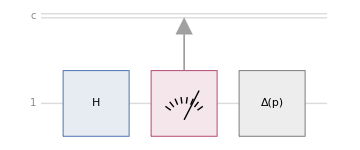

```mathematica
QuantumCircuitOperator[{"H",{1},QuantumChannel[{"Depolarizing",p}]}]["Diagram"]
```

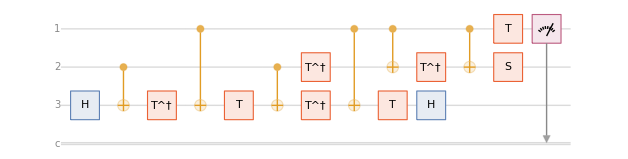

```mathematica
(QuantumCircuitOperator["Toffoli"]/*QuantumMeasurementOperator[{1}])["Diagram","MeasurementWirePosition"->Bottom]
```

#### Book recommendation: Picturing Quantum Processes by Bob Coecke

## Some problem-solving

- create a random 2D pure state
- visualize the Bloch vector
- find the corresponding Bloch spherical and also Cartesian coordinates
- find the state vector in the computational and also Pauli-X basis

- create qubit trine (define as: 0, -1/20-(√3)/2 1,-1/20+(√3)/2 1 
- find their state vector in Pauli-Y basis

- Create a superposition of Bell states 1/(√3)Φ_+-√(2/3)Ψ_-.
- Find its formula.
- After tracing out the 2nd qubit, find the corresponding state of qubit-1. Test if it is a mixed state. 
- Purify the qubit-1 state obtained in the previous state. Show that if tracing out the ancillary qubit from the purified state, one recovers the same state.

- generate two random mixed state in 2D, and calculate their Bures distance

```mathematica
QuantumEntangledQ
```

- show that a Werner state in d=2 is separable if p>=1/2, and entangled if p<1/2
(Hint: you can directly use QuantumEntangledQ, or PPT criterion. The PPT criterion stats that if ρ is separable then all the eigenvalues of the partial transpose of ρ are non-negative. In other words, if the partial transpose of ρ has a negative eigenvalue, ρ is guaranteed to be entangled)

- Show the Schmidt decomposition of this state 1/(√6)(00+01+√2 10-√2 11)
- find the Schmidt coefficients, too.

- generate the W state of 4 qubits. 
- bi-partition the corresponding state into a bipartite system of 2D and 8D (dimensions 2x8)
- find the corresponding Schmidt decomposition and Schmidt coefficients

- given the start graph of 4 vertices (S_4), find the corresponding cluster state. Test if qubit-1 and 2 are entangled or not. Also test, if the overall state is separable or not.

- Given a Werner state with d=2, show that it can be written as a convex combination as follows: (1-λ)/4 I+λΨ_-Ψ_- with λ∈[0,4/3] (Hint: use the replacement rule λ->(1-4p/3))
- find the domain in which ρ is entangled (Hint: PPT criterion stats that if ρ is separable then all the eigenvalues of the partial transpose of ρ are non-negative. In other words, if the partial transpose of ρ has a negative eigenvalue, ρ is guaranteed to be entangled)

```mathematica
r=QuantumState[{"Werner",p,2}]
```

QuantumState[…]

```mathematica
r2=QuantumState[(λ) QuantumState["PsiMinus"]["DensityMatrix"]]+(1-λ)QuantumState[{"UniformMixture",2}]
```

QuantumState[…]

```mathematica
Map[FullSimplify,Normal[r2["DensityMatrix"]]/.{λ->1-4p/3},{2}]==
Normal[r["DensityMatrix"]]
```

True

```mathematica
r2["Transpose",{2}]["Eigenvalues"]
```

{1/4 (1-3 λ),(1+λ)/4,(1+λ)/4,(1+λ)/4}

```mathematica
Reduce[1/4 (1-3 λ)>0,λ]
```

λ<1/3